```mathematica
β[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=
β[ω,δ,t,ϵ1,ϵ2,m]=ReplacePart[ReplacePart[ReplacePart[0*IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t],Table[{a,a},{a,1,2m,2}]->ω+ⅈ*δ-ϵ1],Table[{b,b},{b,2,2m,2}]->ω+ⅈ*δ-ϵ2]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
T2[t_,m_]:= ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
T2[1,7]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=LEFT[ω,δ,t,ϵ1,ϵ2,m]=(*leads[[Round[ω*100+351]]]*)Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=PseudoInverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,15000]; J=J]
```

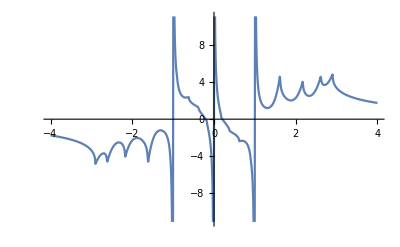

```mathematica
Monitor[Table[{ω,Tr[LEFT[ω,0.0001,1,0,0,9]]/π//Re},{ω,Range[-4,4,0.01]}],ω]//ListLinePlot
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter2/dos/img_agnr_lead.dat",Monitor[Table[{ω,Tr[LEFT[ω,0.0001,1,0,0,9]]/π//Im},{ω,Range[-4,4,0.01]}],ω]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter2/dos/img_agnr_lead.dat

```mathematica
ListPlot[%26,Joined->True]
```

```mathematica
ListPlot[%23,Joined->True]
```

```mathematica
Monitor[Table[Monitor[Table[{ω,-Im[Tr[LEFT[ω,0.0001,1,0,0,n]]]/π},{ω,Range[0,3,0.01]}],ω],{n,9,15,4}],n]
```

```mathematica
Table[Export["~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_semi_"<>ToString[X]<>".dat",Table[{ω,-Im[LEFT[ω,0.0001,1,0,0,7][[X,X]]]},{ω,Range[0,3,0.01]}]],{X,7}]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:= Module[{B= LEFT[ω,δ,t,ϵ,0,m]},PseudoInverse[IdentityMatrix[2m]-B.T2[t,m].B.ConjugateTranspose[T2[t,m]]].B]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:= Module[{B= LEFT[ω,δ,t,ϵ,0,m]},PseudoInverse[IdentityMatrix[2m]-B.T2[t,m].B.ConjugateTranspose[T2[t,m]]].B]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= LEFT[ω,δ,t,ϵ,0,m].T2[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=tr[ω,δ,t,ϵ,m]=Abs[Tr[gdd[ω,δ,t,ϵ,m].T2[t,m].grr[ω,δ,t,ϵ,m].T2[t,m]-T2[t,m].GNON[ω,δ,t,ϵ,m].T2[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter2/9agnr_transm.dat",Table[{ω,tr[ω,0.0001,1,0,9]},{ω,-4,4,0.01}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter2/9agnr_transm.dat

```mathematica
Table[Export["~/Desktop/Thesis/thesis18jun/Images/Chapter2/AGNR_semi_"<>ToString[m]<>"_.dat",Table[{ω,Im[Tr[LEFT[ω,0.0001,1,0,0,m]]]/π},{ω,0,3,0.01}]],{m,7,15,4}]
```

{~/Desktop/Thesis/thesis18jun/Images/Chapter2/AGNR_semi_7_.dat,~/Desktop/Thesis/thesis18jun/Images/Chapter2/AGNR_semi_11_.dat,~/Desktop/Thesis/thesis18jun/Images/Chapter2/AGNR_semi_15_.dat}

```mathematica
Export["~/Desktop/Thesis/thesis/Images/Chapter2/dos_infi_total.dat",Monitor[Table[{ω,-Tr[IL[ω,0.0001,1,0,7]]/π//Im},{ω,Range[0,3,0.01]}],ω]]
```

~/Desktop/Thesis/thesis/Images/Chapter2/dos_infi_total.dat

```mathematica
Table[Export["~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_"<>ToString[X]<>".dat",ParallelTable[{ω,-IL[ω,0.0001,1,0,7][[X,X]]//Im},{ω,Range[-4,4,0.01]}]],{X,7}]
```

{~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_1.dat,~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_2.dat,~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_3.dat,~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_4.dat,~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_5.dat,~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_6.dat,~/Desktop/Thesis/thesis/Images/Chapter2/dos_7agnr_INFI_7.dat}